# Soft NOT

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
SoftNOT[b,w]
```

1-w+b (-1+2 w)

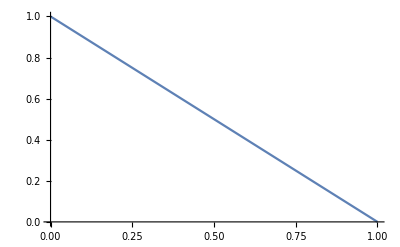

```mathematica
Plot[SoftNOT[b,0],{b,0,1}]
```

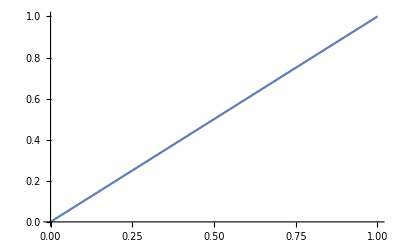

```mathematica
Plot[SoftNOT[b,1],{b,0,1}]
```

```mathematica
Manipulate[Plot[SoftNOT[b,w],{b,0,1},PlotRange->{{0,1},{0,1}}],{w,0,1}]
```

```mathematica
BooleanSoftNOT[b_,w_]:=(b&&w)||(!b&&!w)
```

```mathematica
Harden[b]
```

If[b>0.5,True,False]

```mathematica
BooleanSoftNOT[Harden[0.6],Harden[0.0]]
```

False

```mathematica
Manipulate[
{
Plot[SoftNOT[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2},{1/2}},AxesLabel->Automatic],
DiscretePlot[Boole[BooleanSoftNOT[Harden[b],Harden[w]]],{b,0,1},ExtentSize->Full,AxesLabel->Automatic]
},
{w,0,1}
]
```

```mathematica
hnn=HardNeuralNOT[1][[1]]
```

NetGraph[<>]

```mathematica
Animate[
With[{hnnw=InitializeToConstant[hnn,w]},
Plot[hnnw[b],{b,0,1},PlotRange->{{0,1},{0,1}}]
],
{w,0,1,0.05},
DisplayAllSteps->True
]
```